# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Choi_echo\\QMB_offline.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[10];
```

# Choi Channel Analysis

## Definitions

All reusable functions. Nothing here depends on model parameters or bipartition choice.
Run this chapter once per session.

## Kernel and packing utilities

```mathematica
(* ================================================================ *)
(* BLOCK 0 — Compile target                                          *)
(* ================================================================ *)
$CompileTarget = "WVM";
Needs["Developer`"];
ClearAll[PackC];
PackC[x_] := Developer`ToPackedArray[N[x]];
```

## Spectral unitary

```mathematica
(* ================================================================ *)
(* BLOCK 1 — Spectral unitary                                        *)
(*                                                                   *)
(* Returns a Function[t, U(t)] where                                *)
(*   U(t) = P . Diag(e^{-i λ t}) . P^†                          *)
(* implemented via column scaling to avoid DiagonalMatrix overhead. *)
(*                                                                   *)
(* Inputs:                                                           *)
(*   allvecs — D × D matrix, rows are eigenvectors                    *)
(*   allvals — length-D vector of eigenvalues                          *)
(* ================================================================ *)
ClearAll[SpectralUnitary];
SpectralUnitary[allvecs_, allvals_] :=
  Module[{P = PackC@Transpose[allvecs], Pinv = PackC@Conjugate[allvecs]},
    Function[{t},
      With[{ph = PackC@Exp[-I allvals t]},
        PackC@(Transpose[Transpose[P] * ph] . Pinv)]]];
```

## Environment state

```mathematica
(* ================================================================ *)
(* BLOCK 2 — Environment state                                       *)
(*                                                                   *)
(* Given a global pure state |ψ⟩ on S ⊗ E, returns the reduced   *)
(* density matrix ρ_E = Tr_S[|ψ⟩⟨ψ|] as a packed array.               *)
(*                                                                   *)
(* Inputs:                                                           *)
(*   psi — vector of length dS * dE                               *)
(*   dS  — subsystem Hilbert space dimension (2^La)               *)
(*   dE  — environment Hilbert space dimension (2^Lb)             *)
(* ================================================================ *)
ClearAll[EnvStateFromPsi];
EnvStateFromPsi[psi_, dS_Integer?Positive, dE_Integer?Positive] :=
  PackC@Chop@MatrixPartialTrace[Dyad[psi], 1, {dS, dE}];
```

## Choi state builder

```mathematica
(* ================================================================ *)
(* BLOCK 3 — Choi state builder (Eq. 2 of the paper)               *)
(*                                                                   *)
(* Constructs the Choi-Jamio\[LKSlash]kowski state of the dynamical map E_t.    *)
(*                                                                   *)
(* Protocol (system-environment representation):                    *)
(*   D(t) = Tr_E[ U_R (|Φ+⟩⟨Φ+| ⊗ ρ_E) U_R^† ]           *)
(*   where U_R = I_R ⊗ U acts on R ⊗ S ⊗ E,                  *)
(*   |Φ+⟩ = d_S^{-1/2} ∑_i |i⟩_S |i⟩_R is the maximally    *)
(*   entangled state, and ρ_E is the initial environment state.      *)
(*                                                                   *)
(* This is equivalent to                                             *)
(*   D(t)_{ij,kl} = ⟨i|E_t(|j⟩⟨k|)|l⟩                          *)
(*                                                                   *)
(* Options:                                                          *)
(*   "rhoE" -> n × n matrix (environment density matrix directly)  *)
(*   "psi"  -> dS*dE vector (global pure state; rhoE computed here) *)
(*                                                                   *)
(* Returns a Function[t, D(t)] where D(t) is the dS^2 × dS^2 Choi *)
(* matrix.                                                           *)
(* ================================================================ *)
ClearAll[PhiProjector, ChoiChannelBuilder];

PhiProjector[dS_Integer?Positive] :=
  Module[{phi = PackC@(Flatten[IdentityMatrix[dS]] / Sqrt[dS])},
    PackC@Dyad[phi]];

Options[ChoiChannelBuilder] = {"rhoE" -> None, "psi" -> None};
ChoiChannelBuilder[dS_Integer?Positive, dE_Integer?Positive,
                   unitaryF_Function, opts : OptionsPattern[]] :=
  Module[{rhoE = OptionValue["rhoE"], psi = OptionValue["psi"],
          projPhi, idS},
    If[rhoE === None && psi === None,
      Message[ChoiChannelBuilder::envspec]; Return[$Failed]];
    If[rhoE =!= None && psi =!= None,
      Message[ChoiChannelBuilder::envboth]; Return[$Failed]];
    rhoE = If[rhoE === None, EnvStateFromPsi[psi, dS, dE], rhoE] // PackC;
    projPhi = PhiProjector[dS];        (* |Φ+⟩⟨Φ+| on R ⊗ S *)
    idS     = IdentityMatrix[dS, SparseArray];   (* I_R *)
    Function[{t},
      Module[{U = unitaryF[t], UR, Omega, X},
        UR    = KroneckerProduct[idS, U];          (* I_R ⊗ U(t) *)
        Omega = KroneckerProduct[projPhi, rhoE];   (* |Φ+⟩⟨Φ+| ⊗ ρ_E *)
        X     = UR . Omega . ConjugateTranspose[UR];
        PackC@Chop@MatrixPartialTrace[X, 3, {dS, dS, dE}]   (* trace out E *)
      ]]];

ChoiChannelBuilder::envspec =
  "Provide either \"rhoE\" -> (dE×dE matrix) or \"psi\" -> (dS*dE vector).";
ChoiChannelBuilder::envboth =
  "Provide only one of \"rhoE\" or \"psi\", not both.";
```

## Choi state observables

```mathematica
(* ================================================================ *)
(* BLOCK 4 — Choi state observables                                  *)
(*                                                                   *)
(* All quantities derived from the dS^2 × dS^2 Choi matrix D(t).    *)
(*                                                                   *)
(* ChoiPurity: Tr[D^2]. Bounds: 1/dS^2 (full depolarizing) to 1    *)
(*   (unitary channel). Paper Eq. (3).                               *)
(*                                                                   *)
(* ChoiVNEntropy: S(D) = -Tr[D log D]. Bounds: 0 (unitary) to      *)
(*   log(dS^2) (full depolarizing).                                  *)
(*                                                                   *)
(* ChoiEigenvalues: full spectrum of D(t). Since D(t) is a valid    *)
(*   density matrix (CPTP -> D >= 0, Tr D = 1) all eigenvalues are *)
(*   real in [0,1] and sum to 1. Rank equals minimum Kraus number.  *)
(*                                                                   *)
(* ChoiObservables: single-call aggregator returning an Association.*)
(* ================================================================ *)
ClearAll[ChoiPurity, ChoiVNEntropy, ChoiEigenvalues, ChoiObservables];

ChoiPurity[D_] := Chop@Re@Tr[D . D];

ChoiVNEntropy[D_] :=
  Module[{λ = Select[Re[Eigenvalues[N[D]]], # > 1.*^-14 &]},
    λ = λ / Total[λ];   (* renormalise to absorb numerical noise *)
    -λ . Log[λ]];

ChoiEigenvalues[D_] :=
  Sort[Select[Re[Eigenvalues[N[D]]], # > 1.*^-14 &], Greater];

ChoiObservables[D_] :=
  Module[{λ = Sort[Select[Re[Eigenvalues[N[D]]], # > 1.*^-14 &], Greater],
          λnorm, purity},
    λnorm = λ / Total[λ];
    purity = Re@Tr[D . D];
    <|
      "Purity"      -> Chop@purity,
      "VNEntropy"   -> Chop@(-λnorm . Log[λnorm]),
      "Eigenvalues" -> λ,
      "Rank"        -> Length[λ]
    |>];
```

## Time evolution driver

```mathematica
(* ================================================================ *)
(* BLOCK 5 — Time evolution driver                                   *)
(*                                                                   *)
(* ChoiTimeSeries: maps choiF over tlist and computes selected       *)
(* observables at each step. Returns a list of Associations with    *)
(* key "Time" prepended.                                            *)
(*                                                                   *)
(* Option "Observables" controls what is computed per step:         *)
(*   "All"       — Purity, VNEntropy, Eigenvalues, Rank           *)
(*   "Purity"    — purity only (fastest, no Eigenvalues call)     *)
(*   "Entropy"   — purity + VNEntropy (requires eigenvalues)      *)
(*   "Spectrum"  — all of the above including eigenvalue list      *)
(*                                                                   *)
(* Option "Parallel" -> True/False.                                 *)
(* ================================================================ *)
ClearAll[ChoiTimeSeries];
Options[ChoiTimeSeries] = {"Observables" -> "All", "Parallel" -> True};

ChoiTimeSeries[choiF_Function, tlist_List, OptionsPattern[]] :=
  Module[{obs = OptionValue["Observables"],
          par = TrueQ[OptionValue["Parallel"]],
          stepFn},
    stepFn = Function[{t},
      Module[{D = choiF[t], result},
        result = Switch[obs,
          "Purity",
            <|"Purity" -> ChoiPurity[D]|>,
          "Entropy",
            Module[{λ = Sort[Select[Re[Eigenvalues[N[D]]], # > 1.*^-14 &], Greater]},
              λ = λ / Total[λ];
              <|"Purity"    -> Chop@Re@Tr[D . D],
                "VNEntropy" -> Chop@(-λ . Log[λ])|>],
          _,  (* "All" and "Spectrum" *)
            ChoiObservables[D]
        ];
        Join[<|"Time" -> t|>, result]]];
    If[par,
      ParallelMap[stepFn, tlist, Method -> "CoarsestGrained"],
      Map[stepFn, tlist]]];
```

## Result extraction

```mathematica
(* ================================================================ *)
(* BLOCK 6 — Result extraction helpers                               *)
(* ================================================================ *)
ClearAll[ExtractKey, EigenvalueMatrix];

ExtractKey[results_List, key_String] :=
  {#["Time"], #[key]} & /@ results;

EigenvalueMatrix[results_List] :=
  (* Returns a matrix: rows = time steps, cols = sorted eigenvalues. *)
  (* The Choi matrix dS^2 × dS^2 has at most dS^2 eigenvalues. *)
  With[{ev = (#["Eigenvalues"] & /@ results),
        ts = (#["Time"] & /@ results)},
    Transpose[Prepend[Transpose[ev], ts]]];
```

## Model and Bipartition

Set all physical parameters here. This is the only chapter that changes between runs.
After evaluating this chapter, all downstream chapters run without modification.

## System parameters

```mathematica
(* ================================================================ *)
(* MODEL PARAMETERS                                                  *)
(* Change these for a different model or parameter regime.          *)
(* ================================================================ *)
J  = 1;      (* Ising ZZ coupling *)
hx = 1;      (* transverse field *)
hz = 0.5;    (* longitudinal field (hz ≠ 0 and J ≠ 0 breaks integrability) *)
L  = 6;      (* total chain length *)
```

## Bipartition

```mathematica
(* ================================================================ *)
(* BIPARTITION                                                       *)
(* Probe (subsystem S): first La spins, left end of the open chain. *)
(* Environment (E): remaining Lb = L - La spins.                    *)
(* The paper uses La = 1 (single probe spin) throughout.           *)
(* ================================================================ *)
La = 1;                        (* subsystem size in spins *)
Lb = L - La;                   (* environment size *)
dS = 2^La;                     (* subsystem Hilbert space dimension *)
dE = 2^Lb;                     (* environment Hilbert space dimension *)
```

## Time grid

```mathematica
tMax = 50.;
dt   = 0.1;
tlist = Range[0., tMax, dt];
Print["tlist length: ", Length[tlist]];
```

tlist length: 501

## Hamiltonian

Build and diagonalize the Hamiltonian. Exploits parity symmetry for the Ising model.
For a different model, replace the Hamiltonian definition block only.

## Build

```mathematica
(* ================================================================ *)
(* ISING HAMILTONIAN (open boundary conditions)                     *)
(*   H = ∑_i (hx σ^x_i + hz σ^z_i) - J ∑_i σ^z_i σ^z_{i+1}   *)
(* IsingHamiltonian is defined in QMB_offline.wl.                  *)
(* To switch model: replace this block with a different H.          *)
(* ================================================================ *)
Ha = IsingHamiltonian[hx, hz, J, L, BoundaryConditions -> "Open"];
Print["Hamiltonian dimensions: ", Dimensions[Ha]];
```

Hamiltonian dimensions: {64,64}

## Diagonalize

```mathematica
(* ================================================================ *)
(* Parity block-diagonalize then merge sorted by energy.           *)
(* allvecs: D × D matrix with eigenvectors as rows.               *)
(* allvals: D-vector of eigenvalues.                               *)
(* ================================================================ *)
system = BlockDiagonalize[Ha, Symmetry -> "Parity"];

{eveneigenval, eveneigenvec} =
  Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval, oddeigenvec} =
  Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];

(* Reconstruct full eigenvectors from block-sector vectors *)
{evenMap, oddMap} = buildMaps[L];
neweven = Table[ExpandBlockVector[i, evenMap, "even", L], {i, eveneigenvec}];
newodd  = Table[ExpandBlockVector[i, oddMap,  "odd",  L], {i, oddeigenvec}];

allvecs = Join[neweven, newodd];
allvals = Join[eveneigenval, oddeigenval];
newall  = SortBy[Transpose[{allvals, allvecs}], First];
allvecs = newall[[All, 2]];
allvals = newall[[All, 1]];

Print["Eigensystem: ", Length[allvals], " levels, energy range [",
      N@Min[allvals], ", ", N@Max[allvals], "]"];
Print["Mean level spacing ratio: ", MeanLevelSpacingRatio[allvals]];
```

Eigensystem: 64 levels, energy range [-9.45855, 7.49279]

Mean level spacing ratio: 0.394097

## Environment Initial State

Defines ρ_E, the initial environment state. The Choi matrix D(t) depends on this choice.
For the Haar-averaged Choi echo of the paper (Eq. 7), one would average over many instances
of the random product state defined here. For a single run we fix one realization.

## Random product state (infinite-temperature representative)

```mathematica
(* ================================================================ *)
(* Choose the initial state of the environment.                    *)
(* Here: a random product state of Lb qubits (single realization). *)
(* This corresponds to a single-shot sample of the Haar average    *)
(* in Eq. (7) of the paper.                                        *)
(*                                                                  *)
(* Alternative: set psiE to a specific product state, e.g.        *)
(*   psiE = coherentstate[qubit[0.,0.], Lb]   (all spin-up state) *)
(* ================================================================ *)
SeedRandom[42];
psiE=RandomChainProductState[Lb];

(* Build the global initial state for the full chain S ⊗ E.    *)
(* The subsystem S starts in IS/dS (maximally mixed), consistent  *)
(* with the Choi construction (Eq. 2 of the paper).               *)
(* We do NOT need an explicit global state: rhoE is sufficient     *)
(* for the ChoiChannelBuilder.                                     *)
rhoE=PackC@Dyad[psiE];
Print["rhoE dimensions: ",Dimensions[rhoE],"  (should be {",dE,",",dE,"})"];
Print["Tr[rhoE] = ",N@Tr[rhoE],"  (should be 1)"];
```

rhoE dimensions: {32,32}  (should be {32,32})

Tr[rhoE] = 1.+0. ⅈ  (should be 1)

## Dynamical Map: Choi Matrix

Constructs the time-dependent Choi matrix D(t) via the ChoiChannelBuilder.
The unitary U(t) is built spectrally from the eigensystem computed above.

## Build unitary and Choi function

```mathematica
(* Spectral unitary U(t) = P . Diag(e^{-iλt}) . P^†             *)
unitaryF = SpectralUnitary[allvecs, allvals];

(* Choi matrix function D(t) via system-environment representation  *)
(* (paper Eq. 2, implemented in BLOCK 3).                          *)
choiF = ChoiChannelBuilder[dS, dE, unitaryF, "rhoE" -> rhoE];

(* Sanity check at t = 0: D(0) should be |Φ+⟩⟨Φ+|             *)
(* (unitary channel since U(0) = I), so Tr[D(0)^2] = 1.          *)
D0 = choiF[0.];
Print["t=0 check: Tr[D(0)^2] = ", ChoiPurity[D0], "  (should be 1)"];
Print["t=0 check: Tr[D(0)] = ", N@Re@Tr[D0], "  (should be 1)"];
```

t=0 check: Tr[D(0)^2] = 1.  (should be 1)

t=0 check: Tr[D(0)] = 1.  (should be 1)

## Distribute to parallel kernels

```mathematica
(* Send all objects required inside the time loop to workers. *)
DistributeDefinitions[
  choiF, ChoiPurity, ChoiVNEntropy, ChoiEigenvalues,
  ChoiObservables, MatrixPartialTrace, Dyad
];
```

## Time Evolution

Evaluates D(t) and its derived observables across tlist.
Select "Observables" option to trade accuracy for speed when eigenvalues are not needed.

## Compute

```mathematica
(* ================================================================ *)
(* Options:                                                          *)
(*   "Purity"   — only Tr[D^2], fastest.                           *)
(*   "Entropy"  — Tr[D^2] + S(D), requires one Eigenvalues call.  *)
(*   "All"      — all observables including full spectrum.          *)
(* ================================================================ *)
AbsoluteTiming[
  results = ChoiTimeSeries[choiF, tlist,
    "Observables" -> "All",
    "Parallel"    -> True];
]
```

Global`D::shdw: Symbol D appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

General::stop: Further output of Global`D::shdw will be suppressed during this calculation.

Re::argx: Re called with 0 arguments; 1 argument is expected.

General::stop: Further output of Re::argx will be suppressed during this calculation.

General::stop: Further output of Further output of `1` will be suppressed during this calculation. will be suppressed during this calculation.

ResourceFunction::usermessage: MatrixPartialTrace

Re::argx: Re called with 0 arguments; 1 argument is expected.

ResourceFunction::usermessage: MatrixPartialTrace

General::stop: Further output of ResourceFunction::usermessage will be suppressed during this calculation.

Re::argx: Re called with 0 arguments; 1 argument is expected.

General::stop: Further output of Re::argx will be suppressed during this calculation.

{41.3843,Null}

```mathematica
results[[1]]
```

<|Time→0.,Purity→Re[Tr[$Failed.$Failed]],VNEntropy→-1.0,Eigenvalues→Re[],Rank→0|>

## Results

Plots and derived quantities. The saturation values of purity and entropy are the
key indicators compared against the spectral chaos benchmarks in the paper.

## Choi purity

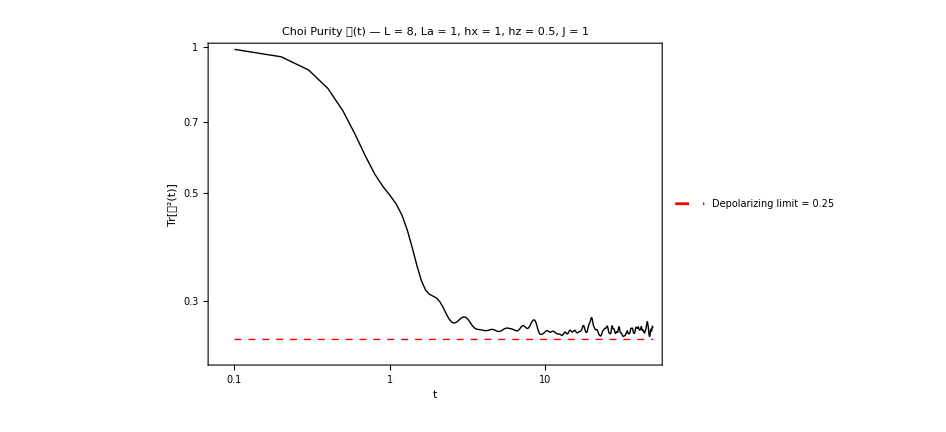

```mathematica
(* ================================================================ *)
(* Choi echo / Choi purity Tr[D(t)^2]                              *)
(*                                                                  *)
(* Bounds:                                                          *)
(*   Upper: 1        (unitary channel, t = 0)                      *)
(*   Lower: 1/dS^2   (completely depolarizing channel)             *)
(*                                                                  *)
(* The red dashed line marks the depolarizing saturation value.    *)
(* ================================================================ *)
purityData = ExtractKey[results, "Purity"];

plotPurity = ListLogLogPlot[purityData,
  Joined        -> True,
  PlotTheme     -> "Detailed",
  PlotLabel     -> Style[
    "Choi Purity 𝒟(t) — L = " <> ToString[L] <>
    ", La = " <> ToString[La] <>
    ", hx = " <> ToString[hx] <>
    ", hz = " <> ToString[hz] <>
    ", J = "  <> ToString[J], 22, Black],
  FrameStyle    -> Directive[Black, FontSize -> 20],
  FrameLabel    -> {Style["t", 18], Style["Tr[\!\(\*SuperscriptBox[\"𝒟\", \"2\"]\)(t)]", 18]},
  PlotStyle     -> Directive[Black, Thick],
  PlotRange     -> All,
  ImageSize     -> 700];

Show[{plotPurity,
  LogLogPlot[1/dS^2, {t, dt, tMax},
    PlotStyle -> Directive[Red, Dashed, Thick],
    PlotLegends -> {Style["Depolarizing limit = " <> ToString[N[1/dS^2]], 16, Red]}]}]
```

## Von Neumann entropy of the Choi state

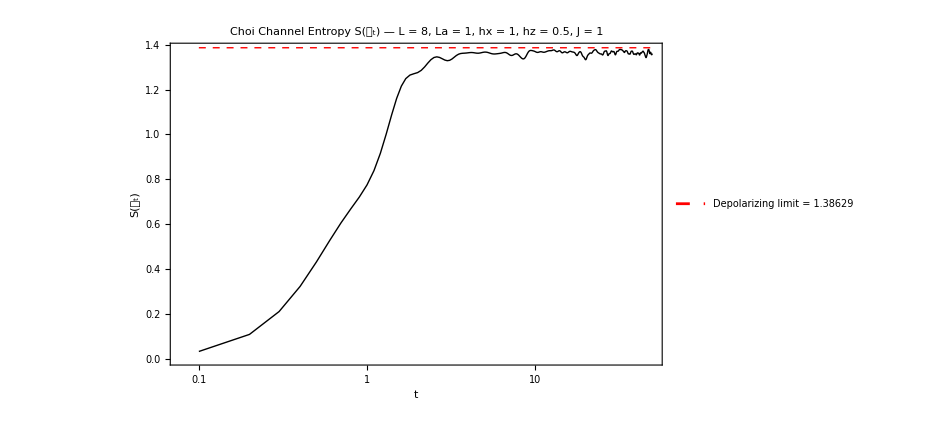

```mathematica
(* ================================================================ *)
(* Channel entropy S(D(t)) = -Tr[D log D]                         *)
(*                                                                  *)
(* Bounds:                                                          *)
(*   Lower: 0         (unitary channel)                            *)
(*   Upper: log(dS^2) (completely depolarizing channel)           *)
(*                                                                  *)
(* The dashed line marks the depolarizing saturation value.        *)
(* ================================================================ *)
entropyData = ExtractKey[results, "VNEntropy"];

plotEntropy = ListLogLinearPlot[entropyData,
  Joined        -> True,
  PlotTheme     -> "Detailed",
  PlotLabel     -> Style[
    "Choi Channel Entropy S(\!\(\*SubscriptBox[\"𝒟\", \"t\"]\)) — L = " <> ToString[L] <>
    ", La = " <> ToString[La] <>
    ", hx = " <> ToString[hx] <>
    ", hz = " <> ToString[hz] <>
    ", J = "  <> ToString[J], 22, Black],
  FrameStyle    -> Directive[Black, FontSize -> 20],
  FrameLabel    -> {Style["t", 18], Style["S(\!\(\*SubscriptBox[\"𝒟\", \"t\"]\))", 18]},
  PlotStyle     -> Directive[Black, Thick],
  PlotRange     -> All,
  ImageSize     -> 700];

Show[{plotEntropy,
  LogLinearPlot[Log[dS^2], {t, dt, tMax},
    PlotStyle -> Directive[Red, Dashed, Thick],
    PlotLegends -> {Style["Depolarizing limit = " <> ToString[N@Log[dS^2]], 16, Red]}]}]
```

## Eigenvalue spectrum of the Choi state

Part::partw: Part 3 of {0.,1.} does not exist.

Part::partw: Part 4 of {0.,1.} does not exist.

Part::partw: Part 5 of {0.,1.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

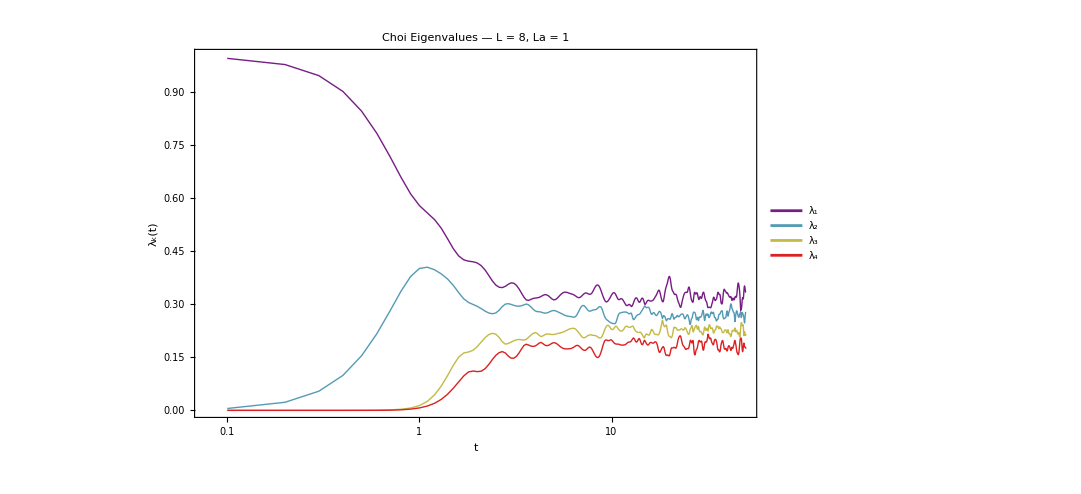

```mathematica
(* ================================================================ *)
(* Eigenvalue spectrum of D(t) as a function of time.              *)
(*                                                                  *)
(* D(t) is a valid density matrix (CPTP map via Choi-Jamio\[LKSlash]kowski).  *)
(* Its eigenvalues are real, non-negative, and sum to 1.           *)
(* Rank = number of Kraus operators in the minimal dilation.       *)
(*                                                                  *)
(* At t = 0: D = |Φ+⟩⟨Φ+| -> rank 1 (unitary channel).          *)
(*                                                                  *)
(* For dS = 2 (La = 1): D is 4×4 -> at most 4 eigenvalues.      *)
(* ================================================================ *)
eigenvalData = Table[
  Prepend[results[[k]]["Eigenvalues"],
          results[[k]]["Time"]], {k, Length[results]}];

(* Plot each eigenvalue track as a function of time *)
nEV = dS^2;   (* max number of eigenvalues for this bipartition *)
evColors = ColorData["Rainbow"] /@ Subdivide[0., 1., nEV - 1];

evTracks = Table[
  {eigenvalData[[k, 1]], eigenvalData[[k, j + 1]]},
  {j, 1, nEV}, {k, Length[results]}];

ListLogLinearPlot[evTracks,
  Joined        -> True,
  PlotTheme     -> "Detailed",
  PlotLabel     -> Style[
    "Choi Eigenvalues — L = " <> ToString[L] <>
    ", La = " <> ToString[La], 22, Black],
  FrameStyle    -> Directive[Black, FontSize -> 20],
  FrameLabel    -> {Style["t", 18], Style["\!\(\*SubscriptBox[\"λ\", \"k\"]\)(t)", 18]},
  PlotStyle     -> ({Directive[evColors[[#]], Thick]} & /@ Range[nEV]),
  PlotRange     -> All,
  ImageSize     -> 800,
  PlotLegends   -> Table[Style["\!\(\*SubscriptBox[\"λ\", " <> ToString[k] <> "]\)", 16], {k, nEV}]]
```

## Saturation values

```mathematica
(* ================================================================ *)
(* Time-averaged saturation values (paper Eq. 8 analogue)          *)
(*                                                                  *)
(* Uses trapezoidal integration over [0, tMax].                    *)
(* Corresponds to the quantity ⟨Tr[D^2]⟩_{Haar,T} of the paper    *)
(* for T = tMax (with a single environment realization here).      *)
(* ================================================================ *)
purityVals  = #["Purity"]   & /@ results;
entropyVals = #["VNEntropy"] & /@ results;

timeAvgPurity = decoherence[purityVals, tlist];   (* reuses decoherence from QMB_offline.wl *)

(* Entropy time average via trapezoidal rule *)
timeAvgEntropy = (1/tMax) *
  Total[Table[(entropyVals[[i]] + entropyVals[[i+1]])/2 * (tlist[[i+1]] - tlist[[i]]),
              {i, 1, Length[tlist] - 1}]];

Print["Time-averaged Choi purity  ⟨Tr[D^2]⟩_T  = ", N@timeAvgPurity];
Print["Time-averaged Choi entropy ⟨S(D)⟩_T   = ", N@timeAvgEntropy];
Print["Depolarizing limit  1/dS^2             = ", N[1/dS^2]];
Print["Depolarizing entropy limit log(dS^2)   = ", N[Log[dS^2]]];
Print["Mean level spacing ratio ⟨r∼⟩              = ",
      N@MeanLevelSpacingRatio[allvals]];
```

Time-averaged Choi purity  ⟨Tr[D^2]⟩_T  = 0.273763

Time-averaged Choi entropy ⟨S(D)⟩_T   = 1.33817

Depolarizing limit  1/dS^2             = 0.25

Depolarizing entropy limit log(dS^2)   = 1.38629

Mean level spacing ratio ⟨r∼⟩              = 0.430907

```mathematica
purityVals  = #["Purity"]   & /@ results;
entropyVals = #["VNEntropy"] & /@ results;

timeAvgPurity = decoherence[purityVals, tlist];   (* reuses decoherence from QMB_offline.wl *)

(* Entropy time average via trapezoidal rule *)
timeAvgEntropy = (1/tMax) *
  Total[Table[(entropyVals[[i]] + entropyVals[[i+1]])/2 * (tlist[[i+1]] - tlist[[i]]),
              {i, 1, Length[tlist] - 1}]];

Print["Time-averaged Choi purity  ⟨Tr[D^2]⟩_T  = ", N@timeAvgPurity];
Print["Time-averaged Choi entropy ⟨S(D)⟩_T   = ", N@timeAvgEntropy];
Print["Depolarizing limit  1/dS^2             = ", N[1/dS^2]];
Print["Depolarizing entropy limit log(dS^2)   = ", N[Log[dS^2]]];
Print["Mean level spacing ratio ⟨r∼⟩              = ",
      N@MeanLevelSpacingRatio[allvals]];
```